```mathematica
ClearAll["Global`*"]
```

## Input

```mathematica
FilePath = "C:\\Users\\labadmin\\Documents\\Micromotion\\data\\250920\\004";
photoncounts = Flatten[Import[FilePath, "Table"]];
```

```mathematica
{bins, counts} = HistogramList[photoncounts, 20]
```

{{0,1000,2000,3000,4000,5000,6000,7000,8000,9000,10000,11000,12000,13000,14000,15000,16000,17000,18000,19000,20000,21000},{171,508,439,455,483,451,428,436,481,478,491,496,449,476,466,487,466,476,466,495,903}}

## Fit

```mathematica
countsPlot = Drop[Drop[counts,1],-1];
ϕList = Table[i 2 π/Length[countsPlot], {i, 0, Length[countsPlot]-1}];
fit = NonlinearModelFit[Transpose[{ϕList, countsPlot}], {A Sin[x 2 + ϕ0] + A0 }, {{A, (Max[countsPlot] - Min[countsPlot])/2}, {f,1}, {ϕ0, 0}, {A0, 2500}}, x]
```

FittedModel[469.842-14.1219 Sin[16.9631-2 x]]

```mathematica
fit["BestFitParameters"]
```

{A→14.1219,f→1.,ϕ0→-16.9631,A0→469.842}

## Output

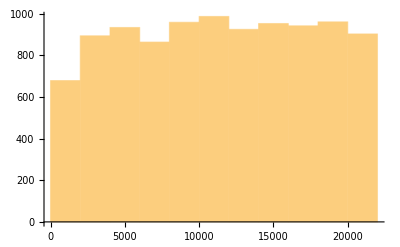

```mathematica
Histogram[photoncounts, 10]
```

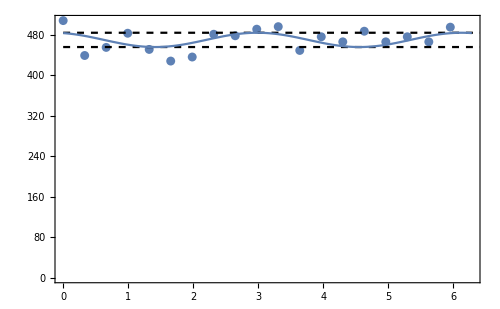

```mathematica
Show[ListPlot[Transpose[{ϕList, countsPlot}]],
	Plot[Evaluate[y = (Abs[A0] + Abs[A])/.fit["BestFitParameters"]],{x,0,10}, PlotStyle-> {Black, Dashed}],
Plot[Evaluate[y = (Abs[A0] - Abs[A])/.fit["BestFitParameters"]],{x,0,10}, PlotStyle-> {Black, Dashed}],
	Plot[fit[x], {x,0,2π}], Frame-> True, PlotRange-> {{0, 2π},{0, Max[countsPlot]}}, ImageSize-> 500, FrameTicks-> {{Automatic,None},{Automatic,None}}, Axes-> False]
```

```mathematica
Rratio = (Abs[2 A]/(Abs[A0] + Abs[A]) )/. fit["BestFitParameters"];
γ = 19.2 10^6;
c = 299792458;
λ = 369 10^-9;
k = (2π)/λ;
θ = π/4;
Dopplershift = -1/4(γ/(c k Cos[θ]) Rratio)^2;
```

```mathematica
Text[Style["The photon fluorescence ratio ΔR/R_max = " <> ToString[Rratio]<>".", FontSize-> 20]]
Text[Style["The Doppler shift Δν/ν = " <> ToString[Dopplershift 10^18]<>" 10^-18.", FontSize-> 20]]
```

The photon fluorescence ratio ΔR/R_max = 0.0583593.

The Doppler shift Δν/ν = -0.0240904 10^-18.

```mathematica
p1 = ListPlot[Transpose[{ϕList, countsPlot}]];
p2 = Plot[Evaluate[y = (Abs[A0] + Abs[A])/.fit["BestFitParameters"]],{x,0,10}, PlotStyle-> {Black, Dashed}];
p3 = Plot[Evaluate[y = (Abs[A0] - Abs[A])/.fit["BestFitParameters"]],{x,0,10}, PlotStyle-> {Black, Dashed}];
	p4 = Plot[fit[x], {x,0,2π}, PlotStyle->Thickness[0.008]];
```

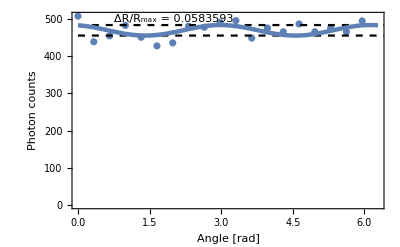

```mathematica
Show[p1, p2, p3, p4, Frame-> True, PlotRange-> {{0, 2π},{0, Max[countsPlot]}}, ImageSize-> 400, FrameTicks-> {{Automatic,None},{Automatic,None}}, Axes-> False, FrameStyle-> Directive[Black, 14], FrameLabel-> {"Angle [rad]", "Photon counts"}, Epilog->{Inset[Framed[Style["ΔR/R_max = " <> ToString[Rratio],14],Background->White],{2, 500}]}]
```